# Pertołów

## Dane

### Nazwy plików konfiguracyjnych

```mathematica
(*fileg="configgLG"; 
*)
```

### Tensor metryczny

```mathematica
(*{g,x}=ReadList[fileg]*)
```

```mathematica
(* kowariantny tensor metryczny gμν - NALEŻY USTAWIĆ!; uwaga! numeracja w tabeli jest od 1 *)
(* wymiar przestrzeni: namx = liczba wierszy = liczba kolumn w tensorze metrycznym *)
nmax=4; 

(* longitudinal gauge, brak przestrzennych elementów pozadiagonalnych w tensorze energii-pędu, czas kosmiczny, zerowa krzywizna *)
g = Table[Which[ n == m && n==1, -(1+2*P*Φ[t,x1,x2,x3]),n == m && n==2, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==3, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]),n == m && n==4, a[t]^2*(1-2*P*Φ[t,x1,x2,x3]), True , 0 ], {n , nmax } , {m , nmax }];
(* tensor metryczny bez perturbacji *)
(*g = Table[Which[ n == m && n==1, -1,n == m && n==2, a[t]^2,n == m && n==3, a[t]^2,n == m && n==4, a[t]^2, True , 0 ], {n , nmax } , {m , nmax }];*)

(* czy zmienne Mukhanova-Sasakiego stosować *)
mMS=True;
(*mMS=False;*)
(* lista zmiennych, w których zapisana jest metryka - NALEŻY USTAWIĆ! *)
x={t,x1,x2,x3};
```

### Lagranżjan

```mathematica
(* liczba pól skalarnych N - NALEŻY USTAWIĆ! *)
lpol=3;

(* pomocniczy wektor z polami skalarnymi ϕ^I *)
(* nazwy pól - MOŻNA USTAWIĆ! (domyślnie ϕ1,ϕ2,...) *)
(*pola=Table[ToExpression["ϕ"<>ToString[I]],{I,1,lpol}]; *)
pola={ϕ,χ,ψ};

(* metryka G w przestrzeni pól (tablica współczynników przy wyrazach z pochodnymi pól w lagranżjanie - zależą od pól) - więc tablica jest symetryczna *)
(* pola bez argumentów - NALEŻY USTAWIĆ! *)
(*fG=Table[If[I<=J,ToExpression["G"<>ToString[I]<>ToString[J]],ToExpression["G"<>ToString[J]<>ToString[I]]][Sequence@@pola],{I ,1,lpol } ,{J ,1,lpol }];*) 
fG=Table[Which[ I == J , 1, True , 0 ],{I ,1,lpol} ,{J ,1,lpol}];

(* lagranżjan z artykułu arXiv:1401.6163v3 L=P(X,pola) *)
(* pola bez argumentów i ogólnie zapisany człon kinetyczny XK, jeżeli potencjał jest wpisywany ogólnie to wstawiamy V[Sequence@@pola] - NALEŻY USTAWIĆ! *)
(*La=fP[XK,Sequence@@pola]; *)
La=XK-V[Sequence@@pola];

(* funkcje i parametry, występujące w lagranżjanie - NALEŻY USTAWIĆ! *)
fun={V->(((Subscript[m, ϕ]*#1)^2+(M*Cos[Δθ/2]*(#2-(#1-Subscript[ϕ, 0])*Tan[(Δθ/Pi)*ArcTan[s*(#1-Subscript[ϕ, 0])]]))^2+(Subscript[m, ψ]*#3)^2+G*(#3*Cos[Δθ/2]*(#2-(#1-Subscript[ϕ, 0])*Tan[(Δθ/Pi)*ArcTan[s*(#1-Subscript[ϕ, 0])]]))^2)/2 &)};
(*fun={V->(((Subscript[m, ϕ]*#1)^2+(M*Cos[Δθ/2]*(#2-(#1-Subscript[ϕ, 0])*Tan[(Δθ/Pi)*ArcTan[s*(#1-Subscript[ϕ, 0])]]))^2+(Subscript[m, ψ]*#3)^2+G*(#3*Cos[Δθ/2]*(#2-Sqrt[(#1-Subscript[ϕ, 0])^2]*Tan[(Δθ/Pi)*ArcTan[s*(#1-Subscript[ϕ, 0])]]))^2)/2 &)};*)

(*param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->2*10^(-4),G->10^(-1),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
(*param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->1.5*10^(-3),G->10^(-1),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)

(*param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->2*10^(-4),G->5*10^(-1),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
(*param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->2*10^(-4),G->9*10^(-1),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
(*param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->2*10^(-4),G->1*10^(-1),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
(*param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->2*10^(-4),G->1*10^(-3),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
(*param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->2*10^(-4),G->1*10^(-2),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
(*param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->2*10^(-5),G->1*10^(-2),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];*)
param=Rationalize[{Subscript[m, ϕ]->10^(-7),Subscript[m, ψ]->10^(-10),M->1*10^(-4),G->1*10^(-2),Subscript[ϕ, 0]->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]}];

(* grawitacyjna część lagranżjanu w teorii f(R) (domyślnie f(R)=R), skalar Ricciego musi być oznaczony przez rr[Sequence@@pola] - NALEŻY USTAWIĆ *)
fR=rr[Sequence@@x];

(* nazwa tworzonego pliku z równaniami - NALEŻY USTAWIĆ! *)
(*sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\pertolow\\3polaTT\\xpsi0,0001_M20_G0,01v2";*)
(*sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\pertolow\\3polaTT\\xpsi0,0001_M2_G0,01";*)
sciezka="C:\\Users\\user\\Documents\\doktorat\\doktorat\\wyniki\\pertolow\\3polaTT\\xpsi0,0001_M10_G0,01";
nazwaplikurow="3polaTT";
```

```mathematica
(* potencjał *)
Block[{tytul=""},
VT[x1_,x2_,x3_]:=V[x1,x2,x3] /.fun /. param;
tytul=mrkWykresy`tytulWykresu[param];
Plot3D[Evaluate[VT[xx,yy,0.0001]],{xx,-246.6,-243.4},{yy,-0.6,1.},AxesLabel->{"ϕ","χ","V"},ColorFunction->Function[{x,y,z},Hue[z]],PlotRange->{10^-10,10^-8},Filling->Bottom,Axes->{True,True,False},PlotLabel->tytul]]
```

-Graphics3D-

## Program

```mathematica
(* wyłączenie komunikatów o użyciu funkcji Inverse przez Solve *)
Off[Solve::ifun];
(* wyłączenie komunikatów o rozwiązywaniu równań algebraicznych i różniczkowych *)
Off[NDSolve::pdord];
```

```mathematica
Needs["mrkFasadaPertolow`"]
```

### Równania

```mathematica
(* tensor metryczny w longitudinal gauge *)
Block[{Lag,potencjal,Masa,ruchurow0,polarow000,ruchurow1,polarow001,polarow011,rowMS1,Ebaza,rowKI1,rowu1,wpisNb,wpisR,wpisB},(
(* gęstość lagranżjanu *)
Lag=Expand[ℒ==Lagrangian[g,x,pola,fG,La,0]];
(* potencjał *)
potencjal=V[Sequence@@pola]==(V[Sequence@@pola] /. fun) ;
(* macierz masy *)
Masa=MacierzMasy[g,x,pola,fG,La,False];
(* równania dla tła *)
ruchurow0=RuchuRownaniakw[g,x,pola,fG,La,0];
polarow000=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,0];
(* równania dla liniowych perturbacji *)
ruchurow1=RuchuRownaniakw[g,x,pola,fG,La,1];
polarow001=PolaRownaniekw[pola,fG,La,fR,0,0,g,x,1];
polarow011=PolaRownaniekw[pola,fG,La,fR,0,1,g,x,1];
(* równania dla zmiennych Mukhanova-Sasakiego *)
rowMS1=If[mMS,MukhanovSasakiRownaniakw[pola,fG,La,g,x,fR,1],False];
(* baza Freneta *)
Ebaza=BazaFreneta[g,x,pola,fG,La,False];
(* równania dla zmiennych krzywizny i izokrzywizny *)
rowKI1=TimeConstrained[PerturbacjeAERownaniakw[pola,fG,La,g,x,fR,mMS,1,True],600,{}];
(* równania dla zmiennych współporuszających się *)
rowu1=WspolporuszajaceRownaniakw[pola,fG,La,g,x,fR,mMS,1,True];
(* zapisanie wyników do notebooka *)
wpisNb={{"Lagranżjan",Lag},{"Potencjał",potencjal},{"Macierz masy",Masa},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Baza Freneta",Ebaza},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikNb[wpisNb,nazwaplikurow,sciezka];
(* zapisanie równań w formie latexowej do pliku txt *)
wpisR={{"Lagranżjan",Lag},{"Potencjał",potencjal},{"Równania ruchu tła",ruchurow0},{"Równanie pola 00 dla tła",polarow000},{"Równania ruchu dla liniowych perturbacji",ruchurow1},{"Równanie pola 00 dla liniowych perturbacji",polarow001},{"Równanie pola 01 dla liniowych perturbacji",polarow011},{"Równania dla zmiennych Mukhanova-Sasakiego",rowMS1},{"Równania dla zmiennych krzywizny i izokrzywizny",rowKI1},{"Równania dla zmiennych współporuszających się",rowu1}};
PlikTexRownania[pola,wpisR,nazwaplikurow,sciezka];
(* zapisanie bazy w formie latexowej do pliku txt *)
wpisB={"Baza Freneta",Ebaza};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"F",sciezka];
wpisB={"Macierz masy",Masa};
PlikTexBaza[pola,wpisB,nazwaplikurow<>"M",sciezka];
)]//AbsoluteTiming
```

20:00:08GMT+2.TimeObject[{20,0,8.00502},TimeZone→2.] Równania ruchu w rzędzie 0

20:00:09GMT+2.TimeObject[{20,0,9.08026},TimeZone→2.] Równania ruchu w rzędzie 0

20:00:09GMT+2.TimeObject[{20,0,9.47172},TimeZone→2.] Równania ruchu w rzędzie 0

20:00:09GMT+2.TimeObject[{20,0,9.85199},TimeZone→2.] Równanie pola 00 w rzędzie 0

20:00:09GMT+2.TimeObject[{20,0,9.99909},TimeZone→2.] Równania ruchu w rzędzie 1

20:00:10GMT+2.TimeObject[{20,0,10.0308},TimeZone→2.] Równania ruchu w rzędzie 1

20:00:10GMT+2.TimeObject[{20,0,10.0621},TimeZone→2.] Równania ruchu w rzędzie 1

20:00:10GMT+2.TimeObject[{20,0,10.3152},TimeZone→2.] Równanie pola 00 w rzędzie 1

20:00:10GMT+2.TimeObject[{20,0,10.5151},TimeZone→2.] Równanie pola 01 w rzędzie 1

20:00:10GMT+2.TimeObject[{20,0,10.6003},TimeZone→2.] Równanie pola 11 w rzędzie 0

20:00:10GMT+2.TimeObject[{20,0,10.6784},TimeZone→2.] Równania ruchu dla zmiennych Mukhanova-Sasakiego

20:00:12GMT+2.TimeObject[{20,0,12.8185},TimeZone→2.] Baza Freneta

20:00:16GMT+2.TimeObject[{20,0,16.9492},TimeZone→2.] Baza Freneta

20:00:17GMT+2.TimeObject[{20,0,17.1497},TimeZone→2.] Pochodne potencjału w zmiennych σ i s

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

20:03:20GMT+2.TimeObject[{20,3,20.0787},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

20:10:18GMT+2.TimeObject[{20,10,18.8822},TimeZone→2.] Równania ruchu dla składowych krzywizny i izokrzywizny

20:20:18GMT+2.TimeObject[{20,20,18.1435},TimeZone→2.] Równania ruchu dla zmiennych współporuszających się

Drop::drop: Cannot drop positions -1 through -1 in {}.

{1211.58,Null}

```mathematica
vv=(((mϕ*x1)^2+(M*Cos[Δθ/2]*(x2-(x1-ϕ0)*Tan[(Δθ/Pi)*ArcTan[s*(x1-ϕ0)]]))^2)/2 /.{mϕ->10^(-7),M->2*10^(-4),ϕ0->-100*Sqrt[6],Δθ->Pi/10,s->5000*Sqrt[3]});
```

```mathematica
NMinimize[{vv, -246.1<x1<-245.05 && -1<x2 <1},{x1,x2},Method->"DifferentialEvolution"]
```

{3.00248×10^-10,{x1→-245.05,x2→0.0159891}}

### Wartości początkowe

```mathematica
Print[TimeObject[Now]];
{tloi,Ntot, tfTot}=Block[{wstepneWP,wstepneWSP,Nall},(
(* szukanie wartości początkowych *)
(* całkowita liczba e-powiększeń - NALEŻY USTAWIĆ! *)
(*Nall=15390.5;*)
Nall=15385.5;
(* wstępne wartości początkowe i współczynniki - NALEŻY USTAWIĆ! *)
(*wstepneWP={-245.01080053350762,0.0097808660,0.}; (* M=10^(-3) *)
wstepneWP={-245.01080053350762,0.009790100,0.}; (* M=2*10^(-4) *)
wstepneWP={-245.01080053350762,0.00979010,0.0001}; (* M=2*10^(-4) *)
wstepneWP={-245.01080053350762,0.009780852,0.01}; (* M=2*10^(-4) *)
wstepneWP={-245.01080053350762,0.0097804805586,1.}; (* M=2*10^(-4) *)
wstepneWP={-245.01080053350762,0.009780599,0.01}; (* M=1.5*10^(-3) *)*)
(*wstepneWP={-245.01080053350762,0.00978906,0.0001}; (* M=2*10^(-4) G=0,5 *)*)
(*wstepneWP={-245.01080053350762,0.00978833,0.0001}; (* M=2*10^(-4) G=0,9 *)*)
(*wstepneWP={-245.01080053350762,0.0097899,0.0001}; (* M=2*10^(-4) G=0,1 *)*)
(*wstepneWP={-245.01080053350762,0.00979010,0.0001}; (* M=2*10^(-4) G=0,01 *)*)
(*wstepneWP={-245.01080053350762,0.00979013,0.0001}; (* M=2*10^(-4) G=0,001 *)*)
(*wstepneWP={-245.05,0.015998721091,0.0001}; (* M=2*10^(-4) G=0,001 *)*)
(*wstepneWP={-245.05,0.015998674,0.0001}; (* M=2*10^(-4) G=0,01 *)*)
(*wstepneWP={-245.01080053350762,0.010550,0.0001}; (* M=2*10^(-5) G=0,01 *)*)
wstepneWP={-245.01080053350762,0.00981871,0.0001}; (* M=1*10^(-4) G=0,01 *)
wstepneWSP={0.,0.,0.};
WartosciPoczatkoweTlo[pola,fG,La,g,x,fR,Nall,wstepneWP,wstepneWSP,fun,param])]
```

23:44:10GMT+2.TimeObject[{23,44,10.7705},TimeZone→2.]

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{ϕ[0.]==-245.011,χ[0.]==0.00981871,ψ[0.]==0.0001,ϕ'[0.]==7.96615×10^-8,χ'[0.]==-1.25525×10^-8,ψ'[0.]==-4.75123×10^-11,nn[0.]==0.}

15385.5

{{{-2920756346386761728/11920928955078125,936385154724121/95367431640625000,1/10000},{4978846453745597/62500000000000000000000,-627622866896961/50000000000000000000000,-1187806723763/25000000000000000000000}},917049442017332822016/59604644775390625,36554949736853651951976448/11920928955078125}

```mathematica
%//N
```

{{{-245.011,0.00979013,0.0001},{7.96618×10^-8,-1.25511×10^-8,-3.02703×10^-13}},15385.5,3.06645×10^9}

```mathematica
{tloi,Ntot, tfTot}=;
```

```mathematica
(* końcowy czas *)
tf=tfTot;
tf=1.2*10^6;
tf=2.5*10^6;
```

```mathematica
(* początkowa wartość liczby e-powiększeń dla tła (N0t) i perturbacji (N0p) - NALEŻY USTAWIĆ! *)
N0t=-7.763;
(*N0t=-12.6865;*)
N0p=N0t;
```

### Tło

```mathematica
Test 
(* czas kosmiczny dla danej liczby e-powiększeń *)
Block[{testN},(
testN={-1,-0.1,0,0.1,0.3,2};
(*testN={-3};*)
CzasN[testN,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{676150.08,766147.92,776147.88,786147.84,806147.88,976153.2}

```mathematica
(* zakresy i czasy wykorzystywane przy rysowaniu wykresów - NALEŻY USTAWIĆ! *)
{m1,m01,pm0,p01,p03}={676150.08,766147.9199999999,776147.88,786147.84,806147.88};(*psi 0*)
{m1,m01,pm0,p01,p03,p2}={1.16833375`24.*^6,1.25833175`24.*^6,1.26833175`24.*^6,1.27833175`24.*^6,1.29833175`24.*^6,1.468337`24.*^6};
m3={968348.`24.};(*N-12*)
{m1,m01,pm0,p01,p03,p2}={676049.88000000000000000000000000000000463571`24.,766047.84000000000000000000000000000000525283`24.,776047.8000000000000000000000000000000053214`24.,786047.76000000000000000000000000000000538997`24.,806047.68000000000000000000000000000000552711`24.,976053.24000000000000000000000000000000669285`24.}; (* M=2 psi=0,0001 N=-8*)
{m1,m01,pm0,p01,p03,p2}={676150.0800000000000000000000000000000046364`24.,766147.92000000000000000000000000000000525351`24.,776147.88000000000000000000000000000000532209`24.,786147.84000000000000000000000000000000539066`24.,806147.8800000000000000000000000000000055278`24.,976153.20000000000000000000000000000000669353`24.}; (* M=10 psi=0,0001 N=-8*)

tzakresBazaM={{m01},{p01}};
tzakresBazaF={m01,p01};
tzakresB={m01,p01};
tB=p03;
(*tN0=pm0;

lista500zc=Join[Range[m01,m002,100],Range[m002,p002,16],Range[p002,p015,77],{tf}];(*{81,250,169}*)
gridzc={{},{m002,pm0,p002,p015},{m01,p015},{m01,p015},{m01,p015}};

lista500={{tf},lista500zc};*)
```

```mathematica
(* efektywna prędkość dźwięku *)
PredkoscDzwiekuEf[g,x,pola,fG,La]
```

1

```mathematica
(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
Block[{zakres={},lista=lista500},
(*lista=Join[listazc,{lista1000[[2]]}];*)
(*lista={{tf},lista1,lista2,lista3,lista4,lista5};*)
zakres={Table[m01,Length[lista]],Join[{p01},Table[p01,Length[lista]-1]]};
(*zakres={Table[m1,Length[lista]],Join[{p2},Table[p2,Length[lista]-1]]};*)
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t,zakrest->zakres];]//AbsoluteTiming
```

{652.589,Null}

```mathematica
TrajektorieTlo[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t,zakrest->{{0},{tf}}];//AbsoluteTiming
```

00:47:06GMT+2.TimeObject[{0,47,6.21314},TimeZone→2.] Czasy

00:47:09GMT+2.TimeObject[{0,47,9.46317},TimeZone→2.] Epilog

00:47:09GMT+2.TimeObject[{0,47,9.49442},TimeZone→2.] Wykres 1

00:47:10GMT+2.TimeObject[{0,47,10.0882},TimeZone→2.] Wykres 2

00:47:10GMT+2.TimeObject[{0,47,10.4007},TimeZone→2.] Wykres 3

00:47:10GMT+2.TimeObject[{0,47,10.6351},TimeZone→2.] Wykres 3D

{8.80832,Null}

```mathematica
(*(* trajektorie inflacyjne w przestrzeni pól *)
Print[TimeObject[Now]];
TrajektorieTlo[pola,fG,La,g,x,fR,wartpocz[[2,1]],wartpocz[[2,3]]+0.2*wartpocz[[2,3]],fun,param,sciezka];//AbsoluteTiming*)
```

```mathematica
(* pochodne pól w zależności od liczby e-powiększeń *)
PochodnePol[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

23:55:30GMT+2.TimeObject[{23,55,30.2262},TimeZone→2.] Liczba e-powiększeń

23:55:30GMT+2.TimeObject[{23,55,30.2352},TimeZone→2.] Wykres 1

23:55:31GMT+2.TimeObject[{23,55,31.3141},TimeZone→2.] Wykres 2

23:55:31GMT+2.TimeObject[{23,55,31.7025},TimeZone→2.] Wykres 3

23:55:32GMT+2.TimeObject[{23,55,32.0184},TimeZone→2.] Wykres energii kinetycznej

{2.14039,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy Freneta, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,zakrest->tzakresBazaF];//AbsoluteTiming
```

23:56:15GMT+2.TimeObject[{23,56,15.774},TimeZone→2.] Prędkości kątowe bazy

23:56:15GMT+2.TimeObject[{23,56,15.841},TimeZone→2.] Liczba e-powiększeń i zmienne

23:56:15GMT+2.TimeObject[{23,56,15.845},TimeZone→2.] Wykres

{32.9469,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń *)
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,{{tf}},fun,param,sciezka,N0->N0t,zakrest->tzakresBazaM, gridt->{}];//AbsoluteTiming
```

23:56:51GMT+2.TimeObject[{23,56,51.7695},TimeZone→2.] Wykres prędkości kątowych bazy

{15.5898,Null}

```mathematica
(* prędkości kątowe, parametryzujące ewolucję czasową bazy wektorów własnych macierzy masy, w zależności od liczby e-powiększeń
z uwzględnieniem produkcji cząstek *)
Block[{grid={{},{}},zakres,lista=lista500},
(*grid={{},{p01},{pm0,p01},{pm0,p005,p01},{m002,pm0,p005,p01},{m01,m002,pm0,p005,p01}};*)
(*lista={{tf},lista1,lista2,lista3,lista4,lista5};*)
zakres={Table[m01,Length[lista]],Join[{p01},Table[p01,Length[lista]-1]]};
PredkosciKatoweBazaMasy[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t,zakrest->zakres,gridt->grid];]//AbsoluteTiming
```

{679.435,Null}

```mathematica
(* kwadraty mas w zależności od liczby e-powiększeń *)
Block[{opisy={}},
(*opisy={Superscript["m","2"],Superscript["M","2"]};*)
Masy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t, legenda->opisy];]//AbsoluteTiming
```

23:57:42GMT+2.TimeObject[{23,57,42.7787},TimeZone→2.] Liczba e-powiększeń i masy

23:57:42GMT+2.TimeObject[{23,57,42.7792},TimeZone→2.] Wykres

{8.06837,Null}

```mathematica
(* kwadraty efektywnych mas w zależności od liczby e-powiększeń (po przejściu do bazy Freneta dla zakrzywionych trajektorii) *)
MasyEfektywne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

20:04:15GMT+2.TimeObject[{20,4,15.6358},TimeZone→2.] Macierz masy w bazie Freneta

20:04:15GMT+2.TimeObject[{20,4,15.6358},TimeZone→2.] Prędkości kątowe bazy

20:04:15GMT+2.TimeObject[{20,4,15.6671},TimeZone→2.] Efektywna macierz masy

20:04:15GMT+2.TimeObject[{20,4,15.968},TimeZone→2.] Liczba e-powiększeń i masy

20:04:15GMT+2.TimeObject[{20,4,15.969},TimeZone→2.] Wykres

$Aborted

```mathematica
Test 
(* wartości bazy wektorów własnych macierzy masy dla pierwotnych pól i bazy Freneta w danej chwili t *)
Block[{testt,bm,bf},(testt=m3;
bm=SetPrecision[BazaMasyTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
Print["BM: ",bm];
bf=SetPrecision[BazaFrenetaTest[testt,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],5];
 Print["BF: ",bf];)]
```

Test

Eigensystem::matsq: Argument {{{9.81166971842118234369×10^-10},{6.19490629295162938935×10^-9},{2.903442967384858×10^-12}},{{«74»},{«75»},{«53»}},{{2.903442967384858×10^-12},{1.83316181315655×10^-11},{9.135630344860322×10^-13}}} at position 1 is not a non-empty square matrix.

Set::shape: Lists {mrkLagrange`Private`wart,mrkLagrange`Private`Mbaza} and Eigensystem[{{{9.81166971842118234369×10^-10},{6.19490629295162938935×10^-9},{2.903442967384858×10^-12}},{{«74»},{«75»},{«53»}},{{2.903442967384858×10^-12},{1.83316181315655×10^-11},{9.135630344860322×10^-13}}}] are not the same shape.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[mrkLagrange`Private`Mbaza].

MapThread::mptd: Object Flatten[mrkLagrange`Private`Mbaza] at position {2, 1} in MapThread[#1→#2&,{Flatten[mrkLagrange`Private`Mbaza],mrkLagrange`Private`wart}] has only 0 of required 1 dimensions.

ReplaceAll::reps: {MapThread[#1→#2&,{Flatten[mrkLagrange`Private`Mbaza],mrkLagrange`Private`wart}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of MapThread[#1→#2&,{Flatten[mrkLagrange`Private`Mbaza],mrkLagrange`Private`wart}].

MapThread::mptd: Object Flatten[mrkLagrange`Private`Mbaza] at position {2, 1} in MapThread[#1→#2&,{Flatten[mrkLagrange`Private`Mbaza],mrkLagrange`Private`Mbaza}] has only 0 of required 1 dimensions.

ReplaceAll::reps: {MapThread[#1→#2&,{Flatten[mrkLagrange`Private`Mbaza],mrkLagrange`Private`Mbaza}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of MapThread[#1→#2&,{Flatten[mrkLagrange`Private`Mbaza],mrkLagrange`Private`Mbaza}].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

BM: Hold[{1.,2.,3.}/.MapThread[#1→#2&,{Flatten[mrkLagrange`Private`Mbaza],mrkLagrange`Private`Mbaza}]]

BF: {{{0.98769},{-0.15643},{-0.000036696}},{{-0.15588},{-0.98421},{0.083853}},{{-0.013154},{-0.082815},{-0.99648}}}

k_turn: 0.00001 ; k(N=3.)=0.000201: {0.000294,0.00287,0.0162}

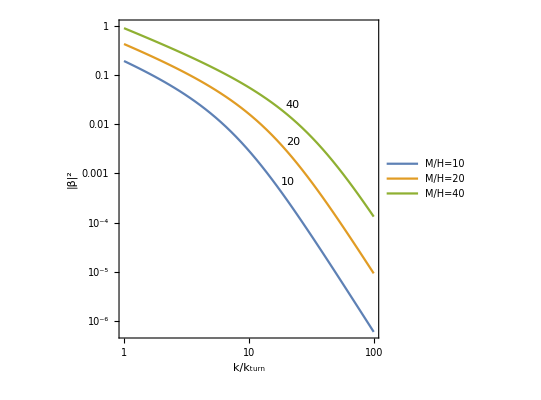

```mathematica
(* liczba obsadzeń w uproszczonej wersji *)
Block[{ml={Subscript[m, ϕ]},mh={M}, kwT,kw, Nkw, r,lo,oznaczenia,legenda},(Nkw=3.;
ml={10^(-7),10^(-7),10^(-7)};mh={10^(-4),2*10^(-4),4*10^(-4)};

{kwT,kw}=Take[WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t],2];

r=MapThread[Sqrt[(kw^2+#2^2)/(kw^2+#1^2)] &,{ml,mh}];
Print["k_turn: ",SetPrecision[kwT,3]," ; k(N=",Nkw,")=",SetPrecision[kw,3],": ",SetPrecision[(((Sqrt[r]-1/Sqrt[r])Sin[Δθ])^2)/4 /. param,3]];
lo=Function[{k,ml,mh},(((Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]]-1/Sqrt[Sqrt[(k^2+mh^2)/(k^2+ml^2)]])Sin[Δθ])^2)/4 /. param];

oznaczenia={10,20,40};
legenda=Map["StyleBox[\"M\",\nFontSlant->\"Italic\"]/StyleBox[\"H\",\nFontSlant->\"Italic\"]="<>ToString[#] &,oznaczenia];
LogLogPlot[Evaluate[MapThread[Labeled[lo[k*kwT,ml[[#1]],mh[[#1]]],#2,{Scaled[0.5],Above}] &, {Range[Length[oznaczenia]],oznaczenia}]],{k,1,1*10^2},Frame->True, AspectRatio->1, FrameLabel->{"StyleBox[\"k\",\nFontSlant->\"Italic\"]/SubscriptBox[ StyleBox[\"k\",\nFontSlant->\"Italic\"], \"turn\"]","|β|^2"},PlotLegends->Placed[legenda,{Left,Bottom}]]
)]
```

```mathematica
(* gęstość energii wyprodukowanych ciężkich cząstek w uproszczonej wersji *)
Block[{mh},(mh={10^(-4), 2*10^(-4), 4*10^(-4), 5*10^(-4), 10^(-3),1.5*10^(-3),1.65*10^(-3),1.7*10^(-3),1.8*10^(-3),1.9*10^(-3), 2*10^(-3)};
Print["l ", N[mh^4*Sin[Δθ]^2/(24*Pi^2) /. param]];
Print["h ", N[mh^4*Sin[Δθ]^2/(16*Pi^2) /. param]];)]
```

l {4.03138×10^-20,6.45021×10^-19,1.03203×10^-17,2.51961×10^-17,4.03138×10^-16,2.04089×10^-15,2.98806×10^-15,3.36705×10^-15,4.23198×10^-15,5.25373×10^-15,6.45021×10^-15}

h {6.04707×10^-20,9.67531×10^-19,1.54805×10^-17,3.77942×10^-17,6.04707×10^-16,3.06133×10^-15,4.48209×10^-15,5.05057×10^-15,6.34797×10^-15,7.8806×10^-15,9.67531×10^-15}

```mathematica
(* wykresy elementów bazy wektorów własnych macierzy masy *)
WykresyBazaMasy[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

23:58:01GMT+2.TimeObject[{23,58,1.69682},TimeZone→2.] Liczba e-powiększeń i baza wektorów własnych macierzy masy

23:58:01GMT+2.TimeObject[{23,58,1.70232},TimeZone→2.] Wykres wierszy 1

23:58:16GMT+2.TimeObject[{23,58,16.0224},TimeZone→2.] Wykres wierszy 2

23:58:16GMT+2.TimeObject[{23,58,16.5157},TimeZone→2.] Wykres wierszy 3

23:58:16GMT+2.TimeObject[{23,58,16.9085},TimeZone→2.] Wykres kolumn 1

23:58:17GMT+2.TimeObject[{23,58,17.3318},TimeZone→2.] Wykres kolumn 2

23:58:17GMT+2.TimeObject[{23,58,17.7577},TimeZone→2.] Wykres kolumn 3

{16.5514,Null}

```mathematica
(* wykresy elementów bazy Freneta *)
WykresyBaza[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];//AbsoluteTiming
```

23:58:20GMT+2.TimeObject[{23,58,20.7599},TimeZone→2.] Liczba e-powiększeń i baza

23:58:20GMT+2.TimeObject[{23,58,20.7629},TimeZone→2.] Wykres wierszy 1

23:58:53GMT+2.TimeObject[{23,58,53.6751},TimeZone→2.] Wykres wierszy 2

23:58:57GMT+2.TimeObject[{23,58,57.0701},TimeZone→2.] Wykres wierszy 3

23:58:57GMT+2.TimeObject[{23,58,57.5239},TimeZone→2.] Wykres kolumn 1

23:58:57GMT+2.TimeObject[{23,58,57.967},TimeZone→2.] Wykres kolumn 2

23:58:58GMT+2.TimeObject[{23,58,58.4841},TimeZone→2.] Wykres kolumn 3

{38.2666,Null}

```mathematica
Test 
(* wykresy funkcji zależnych od pól i liczby e-powiększeń oraz ich pierwszych pochodnych w zależności od liczby e-powiększeń *)
Block[{funkcje,opisy,
Lao},(
(*funkcje={Map[#'[x[[1]]]/Symbol["nn"]'[x[[1]]] &, pola]};
opisy={{"wkladPM",Map[ToString[#]<>"'(t)/H" &, pola]}};*)

(*(* lista współczynników oddziaływania w formie {{C_σs1, C_σs2, ...}, {C_s1σ, C_s1s2, ...}, ...} *)
funkcje=Simplify[WspolczynnikiOddzialywaniaAE[pola,fG,La,g,x,fR,mMS,1]];
opisy={{"C1","coefficients",{"C_σs1","C_σs2"}},{"C2","coefficients",{"C_s1σ","C_s1s2"}},{"C3","coefficients",{"C_s2σ","C_s2s1"}}};*)

funkcje={{Symbol["nn"]'[x[[1]]]}};
opisy={{"H","",{"H"}}};

(*Lao=Take[mrkLagrange`lagrangianO[g,x,pola,fG,La],{4}][[1]]/. Symbol["P"]->0;*)

(*funkcje={{Abs[Symbol["τ"][x[[1]]]]}};
opisy={{"tau","",{"tau"}}};*)

WykresyTestoweTlo[funkcje,opisy,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0t];)]//AbsoluteTiming
```

Test

23:59:10GMT+2.TimeObject[{23,59,10.6369},TimeZone→2.] Liczba e-powiększeń

23:59:10GMT+2.TimeObject[{23,59,10.6399},TimeZone→2.] Wykres 1

{4.41736,Null}

### Perturbacje

```mathematica
(* widma *)
(* widma w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->3.,norm->"t",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

```mathematica
(* perturbacje w zależności od liczby e-powiększeń *)
PerturbacjeB[pola,fG,La,g,x,fR,tloi,lista500zc,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"wsp",5.5},NkwNorm->0.,norm->"",tftot->tfTot,baza->"",RS->False,pertu->False];//AbsoluteTiming
```

04:42:48GMT+2.TimeObject[{4,42,48.5409},TimeZone→2.] Liczba e-powiększeń i widma

kw 0.0000549728

tf A {28.4502,4.50617}

tf {Re,Im} {{{27.4032,7.02014},{4.34746,1.08329}},{{2.9669,0.628479},{0.473532,0.085902}}}

04:42:48GMT+2.TimeObject[{4,42,48.7655},TimeZone→2.] Wykres perturbacji

04:42:59GMT+2.TimeObject[{4,42,59.0633},TimeZone→2.] Wykres wierszy 1

04:43:01GMT+2.TimeObject[{4,43,1.73833},TimeZone→2.] Wykres wierszy 2

04:43:03GMT+2.TimeObject[{4,43,3.93532},TimeZone→2.] Wykres kolumn 1

04:43:05GMT+2.TimeObject[{4,43,5.93501},TimeZone→2.] Wykres kolumn 2

04:43:08GMT+2.TimeObject[{4,43,8.13598},TimeZone→2.] Wykres Re

04:43:14GMT+2.TimeObject[{4,43,14.92},TimeZone→2.] Wykres Im

{452.07,Null}

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
Block[{grid={},opisy={},zakres={},lista={{tf}},listaNkw},
(*grid={{},{p01},{pm0,p01},{pm0,p005,p01},{m002,pm0,p005,p01},{m01,m002,pm0,p005,p01}};*)
opisy={"0.001","0.005","0.01","0.1","0.5"};
opisy={"0.1","0.5","1"};
opisy={"1","2","10","20"};
listaNkw=Map[{"wsp",#} &, {0.001,0.005,0.01,0.1,0.5}];
listaNkw=Map[{"wsp",#} &, {0.1,0.5,1}];
listaNkw=Map[{"wsp",#} &, {1.,2.,10.,20.}];
lista=Table[{tf},Length[listaNkw]];
zakres={Table[m1,Length[lista]],Join[{p2},Table[p2,Length[lista]-1]]};
WidmaB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->listaNkw,NkwNorm->0.,norm->"h",tftot->tfTot,baza->"M",RS->True,pertu->False,zakrest->zakres,gridt->grid,legenda->opisy];]//AbsoluteTiming
```

00:06:31GMT+2.TimeObject[{0,6,31.5892},TimeZone→2.]

kw {9.99506×10^-6,0.0000199901,0.0000999506,0.000199901}

tf {{1.13139,0.000489418,0.286279},{1.45082,0.00226814,0.39999},{2.9107,0.257948,2.68688},{8.42506,1.92507,8.42458}}

00:45:07GMT+2.TimeObject[{0,45,7.94296},TimeZone→2.] Wykres widm 1

00:45:33GMT+2.TimeObject[{0,45,33.7557},TimeZone→2.] Wykres widm 2

00:46:40GMT+2.TimeObject[{0,46,40.9629},TimeZone→2.] Wykres widm 3

00:46:41GMT+2.TimeObject[{0,46,41.9785},TimeZone→2.] Wykres widm

00:46:43GMT+2.TimeObject[{0,46,43.9785},TimeZone→2.] Wykres wierszy 1

$Aborted

```mathematica
(* widma w bazie Freneta w zależności od liczby falowej *)
Print[TimeObject[Now]];
Widma[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"F"];//AbsoluteTiming
```

$Aborted

```mathematica
(* widma w bazie wektorów własnych macierzy masy w zależności od liczby falowej *)
Print[TimeObject[Now]];
WidmaB[pola,fG,La,g,x,fR,tloi,{{tf},listatfn1},fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,norm->"h",tftot->tfTot,baza->"M",RS->True,pertu->False,zakrest->{{0.,0.},{tf,tf}}];//AbsoluteTiming
```

```mathematica
(* wzmocnienia widma perturbacji krzywizny w zależności od liczby falowej *)
Print[TimeObject[Now]];
Block[{punkty,
(*lista={{m01},{tf}},*)
lista={{tf}},
(*opisy={ToString["ℛ",TraditionalForm]<>" (-0.1)",ToString[Subscript["𝒮","2"],TraditionalForm]<>" (-0.1)",ToString["ℛ",TraditionalForm]<>" (12)",ToString[Subscript["𝒮","2"],TraditionalForm]<>" (12)"}*)
opisy={}
},
punkty=Map[{"wsp", #} &, Join[Range[0.1,3.,0.1],Range[3.,20.,0.1]]];
(*punkty=Map[{"wsp", #} &, Join[Range[3.,10.,1.]]];*)
(*punkty=Map[{"wsp", #} &, {0.001,0.005,0.01,0.05,0.1,0.2,0.3,0.4,0.5,1.}];*)
(*punkty=Map[{"wsp", #} &, Join[Range[0.001,0.01,0.001],Range[0.01,0.1,0.01],Range[0.1,0.5,0.1]]];*)
(*punkty=Map[{"wsp", #} &, {0.1, 0.5, 1., 2., 5., 10.}];*)
(*punkty=Map[{"wsp", #} &, {0.1,0.3,0.5,0.7,1.,2.,2.5,3.,4.,5.,6.,7.,8.,9.,10.}];
punkty=Map[{"wsp", #} &, {0.1,1.,2.,10.}];*)
WzmocnienieB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->punkty, NkwNorm->Table[0.,Length[lista]],baza->"M",nrwidm->{1,3},legenda->opisy]]//AbsoluteTiming
```

00:03:28GMT+2.TimeObject[{0,3,28.671},TimeZone→2.]

00:03:28GMT+2.TimeObject[{0,3,28.671},TimeZone→2.]Rozwiązanie 1

ll

00:03:33GMT+2.TimeObject[{0,3,33.1458},TimeZone→2.] Wykres widm(k) - wzmocnienia(k)

{4.91437,Null}

```mathematica
Test 
(* widma dla podanej bazy *)
Print[TimeObject[Now]];
Block[{baza},(
baza={};
baza={{1,0,0},{0,1,0},{0,0,1}};
WidmaTest[baza,pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p];)]//AbsoluteTiming
```

16:15:53GMT+2.TimeObject[{16,15,53.1763},TimeZone→2.]

16:15:53GMT+2.TimeObject[{16,15,53.1919},TimeZone→2.] Perturbacje ℛ i 𝒮

16:15:54GMT+2.TimeObject[{16,15,54.8795},TimeZone→2.] Widma

16:15:55GMT+2.TimeObject[{16,15,55.0357},TimeZone→2.] Liczba e-powiększeń i widma

16:15:55GMT+2.TimeObject[{16,15,55.2857},TimeZone→2.] Wykres

{4.00844,Null}

```mathematica
(* korelacje względne *)
Print[TimeObject[Now]];
KorelacjeWzgledne[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->True,Nkw->{"N",3.}];//AbsoluteTiming
```

02:15:31GMT+2.TimeObject[{2,15,31.8027},TimeZone→2.]

02:15:31GMT+2.TimeObject[{2,15,31.8087},TimeZone→2.] Korelacje

02:15:31GMT+2.TimeObject[{2,15,31.8097},TimeZone→2.] Korelacje względne

02:15:31GMT+2.TimeObject[{2,15,31.8167},TimeZone→2.] Liczba e-powiększeń i względne korelacje

02:15:31GMT+2.TimeObject[{2,15,31.8167},TimeZone→2.] Wykres

NDSolve::vdobj: Encountered Qσkw[0.]==117382., which is not a valid NDSolve`StateData expression.

General::stop: Further output of NDSolve::vdobj will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {NDSolve`ProcessSolutions[Qσkw[0.]==117382.],NDSolve`ProcessSolutions[Qσkw[0.]==117382.],NDSolve`ProcessSolutions[Qσkw[0.]==117382.]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{0.512465,Null}

```mathematica
Print[TimeObject[Now]];
Korelacje[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t,N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->3.,norm->"h",tftot->tfTot];//AbsoluteTiming
```

01:40:34GMT+2.TimeObject[{1,40,34.8096},TimeZone→2.]

01:40:34GMT+2.TimeObject[{1,40,34.8252},TimeZone→2.] Korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8428},TimeZone→2.] Liczba e-powiększeń i korelacje

01:40:34GMT+2.TimeObject[{1,40,34.8443},TimeZone→2.] Wykres

{1.56311,Null}

```mathematica
Test
(* liczby falowe dla N=0 (k1) i N=Nkw (k2) w momencie przekraczania promienia Hubble'a: k=aH; {k1, k2, k1-k2, k2/k1} *)
Block[{Nkw},(Nkw=1.;
WektorFalowyTest[Nkw,pola,fG,La,g,x,fR,tloi,tf,fun,param,N0t])]
```

Test

{9.99506045850382049×10^-6,0.000027168517603223311247,-0.000017173457144719490757,2.7181944237374045908}

```mathematica
(* liczby obsadzeń *)
(* liczba obsadzeń w zależności od liczby e-powiększeń *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",3.},NkwNorm->0.,zakrest->tzakresB];//AbsoluteTiming
```

05:06:21GMT+2.TimeObject[{5,6,21.3583},TimeZone→2.]

05:14:04GMT+2.TimeObject[{5,14,4.10504},TimeZone→2.] Liczba e-powiększeń i liczba obsadzeń

{3.50943×10^-9,1.49779×10^-6}05:14:04GMT+2.TimeObject[{5,14,4.13455},TimeZone→2.]

{1.33444×10^-10,1.99601×10^-10}05:14:04GMT+2.TimeObject[{5,14,4.16809},TimeZone→2.]

{0.00644601,0.00657539}05:14:04GMT+2.TimeObject[{5,14,4.19861},TimeZone→2.]

05:14:04GMT+2.TimeObject[{5,14,4.19911},TimeZone→2.] Wykres

{475.446,Null}

```mathematica
(* liczba obsadzeń w zależności od liczby falowej *)
Print[TimeObject[Now]];
LiczbaObsadzen[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"",0.},NkwNorm->0.,zakrest->{tB}];//AbsoluteTiming
```

03:26:01GMT+2.TimeObject[{3,26,1.53742},TimeZone→2.]

03:26:01GMT+2.TimeObject[{3,26,1.67498},TimeZone→2.] Liczba obsadzeń

kwNorm: {0.463267,0.829206}03:26:03GMT+2.TimeObject[{3,26,3.71264},TimeZone→2.]

1.5: {1.02366,0.375015}03:26:05GMT+2.TimeObject[{3,26,5.92366},TimeZone→2.]

2: {0.365702,0.228618}03:26:08GMT+2.TimeObject[{3,26,8.31438},TimeZone→2.]

10: {0.0139638,0.0138118}03:26:14GMT+2.TimeObject[{3,26,14.0065},TimeZone→2.]

20: {0.00205275,0.00223467}03:26:23GMT+2.TimeObject[{3,26,23.8839},TimeZone→2.]

03:26:23GMT+2.TimeObject[{3,26,23.8844},TimeZone→2.] Wykres

$Aborted

```mathematica
Test
(* gęstość energii wyprodukowanych na zakręcie cząstek w chwili t0 *)
Print[TimeObject[Now]];
GestoscEnergiiCzastekTest[pola,fG,La,g,x,fR,tloi,tf,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS, t0->tN0]//AbsoluteTiming
```

Test

04:56:04GMT+2.TimeObject[{4,56,4.98974},TimeZone→2.]

04:56:13GMT+2.TimeObject[{4,56,13.7468},TimeZone→2.] Gęstości energii wyprodukowanych cząstek

{{0.000099552,0},{0,0.00098715}}

{9.9951×10^-6,{0.00010005,0.0009872}}

4.45893×10^-14

8.78729×10^-14

$Aborted

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny: {kw,kw2,kw-kw2,indeks} *)
Print[TimeObject[Now]];
IndeksSpektralny[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",0.1},baza->"F"]//AbsoluteTiming
```

$Aborted

```mathematica
(* indeks spektralny n_s dla perturbacji krzywizny i izokrzywizny *)
Print[TimeObject[Now]];
Block[{punkty,punkty2,lista={{tf}}},
punkty=Map[{"wsp", #} &, Join[Range[0.1,3.,0.1],Range[3.,10.,0.1]]];
(*punkty=Map[{"wsp", #} &, {0.1, 0.5, 1., 2., 5., 10.}];*)
(*punkty=Map[{"wsp", #} &, {0.1,0.3,0.5,0.7,1.,2.,2.5,3.,4.,5.,6.,7.,8.,9.,10.}];*)
(*punkty=Map[{"wsp", #} &, {0.1,1.,2.,10.}];*)
punkty2=Table[10^(-6),Length[punkty]];
IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,lista,fun,param,sciezka,N0->N0t, N0P->N0p,MS->mMS,Nkw->punkty,Nkw2->punkty2, NkwNorm->Table[0.,Length[lista]],baza->"M",nrwidm->{1,3}]]//AbsoluteTiming
```

19:54:47GMT+2.TimeObject[{19,54,47.9424},TimeZone→2.]

19:54:47GMT+2.TimeObject[{19,54,47.958},TimeZone→2.]Rozwiązanie 1

19:54:49GMT+2.TimeObject[{19,54,49.7737},TimeZone→2.] Wykres ns(k)

{2.16656,Null}

```mathematica
(* indeksy spektralne dla perturbacji oraz wzmocnienie perturbacji krzywizny *)
Block[{Nk=0.1,k1,k2,dk,indeksns,PRf,opisy,wartosci,nazwaplikuwp},(
(* liczby falowe i indeksy spektralne *)
{k1,k2,dk,indeksns}=IndeksSpektralnyB[pola,fG,La,g,x,fR,tloi,{tf},fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.},Nkw2->{"N",Nk},baza->"F"];
(* wzmocnienie perturbacji krzywizny *)
PRf=Wzmocnienie[pola,fG,La,g,x,fR,tloi,tf,fun,param,N0->N0t, N0P->N0p,MS->mMS,Nkw->{"N",0.}, NkwNorm->0.];
(* zapisanie wyników *)
opisy=Join[ Map[#[[1]] &, param], {Subscript[N,"0t"],Subscript[N,"0p"],Subscript[N,"tot"]}, Map[Subscript[#,0]&, pola], Map[Subscript[OverDot[#],0]&, pola], {Subscript[k,0],Subscript[k,Nk],Δ k}, {Subscript[n,"s"](Subscript[P,ℛ])},Map[Subscript[n,"s"](Subscript[P,Subscript[𝒮,#]]) &, Range[lpol-1]], {λ}];
(*wartosci=Flatten[{Map[NumberForm[Round[#[[2]],0.01],NumberPoint->","] &, param], {N0t,N0p},Map[NumberForm[Round[#,0.001],NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];*)
wartosci=Flatten[{Map[ScientificForm[If[Element[#[[2]],Rationals],N[#[[2]]],#[[2]]], 2, NumberMultiplier->"*",NumberPoint->","] &, param], {NumberForm[N0t,NumberPoint->","],NumberForm[N0p,NumberPoint->","]},Map[ScientificForm[If[Element[#,Rationals],N[#],#], 3, NumberMultiplier->"*",NumberPoint->","] &, Flatten[{Ntot,tloi,k1,k2,dk,indeksns,PRf}]]}];
(* nazwa tworzonego pliku z wartościami początkowymi i indeksem spektralnym *)
nazwaplikuwp=nazwaplikurow<>"_dane.txt";
PlikTexTabela[opisy,wartosci,nazwaplikuwp,sciezka];)]//AbsoluteTiming
```

{0.0324733,Null}

```mathematica
Quit[]
```